{I1→-(ⅈ I0)/(-ⅈ+Cc R ω),I2→(Cc I0 R ω)/(-ⅈ+Cc R ω)}

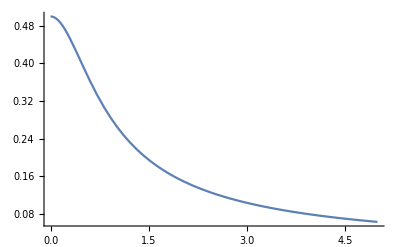

```mathematica
sol=Solve[{I0==I1+I2,I2 1/(I ω Cc)==R I1},{I1,I2}][[1]]

Plot[Abs[I1 R/.sol/.{I0 ->0.001,R->500,Cc->5 10^-12,ω->2 Pi f}],{f,0,500000000},PlotRange->All]
```

{I1→Function[{t},-ⅇ^(-t/(Cc R)) I0 (-ⅇ^(1/(1000000000 Cc R)) HeavisideTheta[-1/1000000000+t]+ⅇ^(t/(Cc R)) HeavisideTheta[-1/1000000000+t]+HeavisideTheta[t]-ⅇ^(t/(Cc R)) HeavisideTheta[t])],I2→Function[{t},-ⅇ^(-t/(Cc R)) I0 (ⅇ^(1/(1000000000 Cc R)) HeavisideTheta[-1/1000000000+t]-HeavisideTheta[t])]}

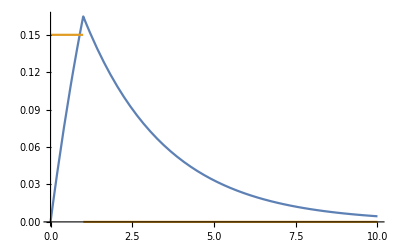

```mathematica
sol=DSolve[{I0(HeavisideTheta[t]-HeavisideTheta[t-10^-9])==I1[t]+I2[t],I2[t]/Cc==R I1'[t],I1[0]==0},{I1,I2},t][[1]]
Plot[{R I1[t 10^-9]/.sol/.{I0 ->0.001,R->500,Cc->5 10^-12},0.15(HeavisideTheta[t]-HeavisideTheta[t-1])},{t,0,10},PlotRange->All,AxesOrigin->{0,0}]
```

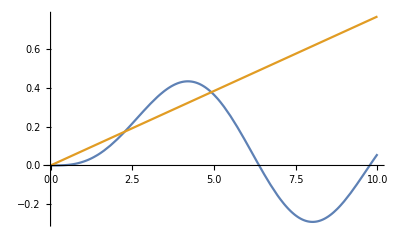

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[BesselJ[3,x]==x/13,x]

{x→2.26989}

```mathematica
Plot[{BesselJ[3,x],1/13x},{x,0,10}]

Solve[BesselJ[3,x]==1/13x,x]

FindRoot[BesselJ[3,x]==1/13x,{x,2}]
```

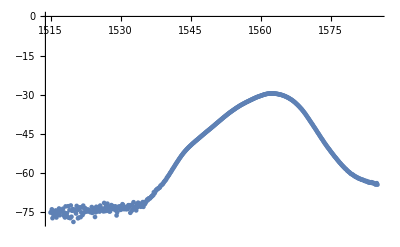

```mathematica
spec=Import["Data.xlsx",Path->NotebookDirectory[]][[1]];

ListPlot[spec]
```

Домашнее задание

Изучить еще раз оператор Part!

1)* Найти аналитически сигнал снимаемый с фотодиода, если на фотодиод падает оптический импульс по форме являющимся равносторонним треугольником с основанием 2τ (τ - время возрастания интенсивности, τ - время убывания). Граничные условия периодические: через 10τ приходит новый импульс, т.е. все токи в контуре будут повторяться с периодом 10τ
2) В файле “Data.xlsx” на листе “HomeWork. Pulse” представлена измеренная форма импульса на выходе из лазера. Известно, что PRR - 16.5 МГц, средняя мощность на выходе 19 мВт. Найти точно пиковую мощность импульса. *Учесть, что в выходном излучении присутствует доля непрерывного излучения.
3)* Аппроксимировать импульс из предыдущей задачи гауссовым. Использовать FindFit, нарисовать одновременно и точки и аппроксимацию. Вывести вычисленные параметры аппроксимации.
4) Дан элемент, спектр отражения которого приведен на листе “HomeWork. VBG” (в процентах). Найти отраженный спектр “Spectrum” от данного элемента.
5) Изучить https://en.wikipedia.org/wiki/Finite_difference_coefficient . Составить оператор, который дифференцирует дискретную функцию с 1, 2 и 4 порядком точности. *Учесть различные коэффициенты дифференциалов на границе области определения функции. Применить оператор, например, к “Spectrum”. Возможно, здесь пригодится функция ListConvolve